# Practical 5 :

## To Solve system of ordinary differential equation

## Question 1: x’[t]==y[t] y’[t]==-y[t] + 6x[t], x[0]==1, y[0] == -2

{x'[t]==y[t],y'[t]==6 x[t]-y[t],x[0]==1,y[0]==-2}

{{x[t]→1/5 ⅇ^(-3 t) (4+ⅇ^(5 t)),y[t]→2/5 ⅇ^(-3 t) (-6+ⅇ^(5 t))}}

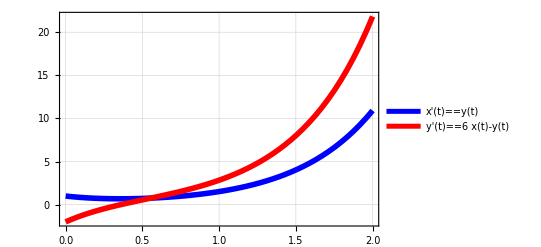

```mathematica
eq1 = {x'[t]==y[t], y'[t]==-y[t]+6*x[t], x[0]==1, y[0]==-2}
DSolve[eq1, {x[t],y[t]}, t]
Plot[Evaluate[{x[t],y[t]} /. %], {t,0,2},PlotLegends->{eq1},PlotStyle->{{Blue,Thickness[0.01]},{Red,Thickness[0.01]}},Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed]]
```

## Question 2: x’[t]==6*x[t] - 3*y[t] y’[t]==2*x[t]+ y[t]

{{x[t]→ⅇ^(3 t) (-29+30 ⅇ^t),y[t]→ⅇ^(3 t) (-29+20 ⅇ^t)}}

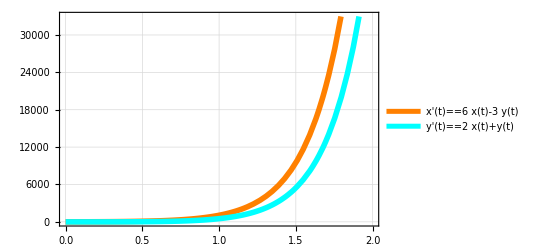

```mathematica
eq2 :={x'[t]==6*x[t] - 3*y[t], y'[t]==2*x[t]+ y[t], x[0]==1, y[0]==-9};
DSolve[eq2, {x[t],y[t]}, t]
Plot[Evaluate[{x[t],y[t]} /. %], {t,0,2},PlotLegends->{eq2},PlotStyle->{{Orange,Thickness[0.01]},{Cyan,Thickness[0.01]}},Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed]]
```

## Question 3: x’[t]==6*x’[t] - 3*y[t] y’[t]==2*x[t]+ y[t]

{{x[t]→-1/290 ⅇ^(t/2-1/2 √(29/5) t) (-145-59 √145-145 ⅇ^(√(29/5) t)+59 √145 ⅇ^(√(29/5) t)),y[t]→-1/58 ⅇ^(t/2-1/2 √(29/5) t) (261-5 √145+261 ⅇ^(√(29/5) t)+5 √145 ⅇ^(√(29/5) t))}}

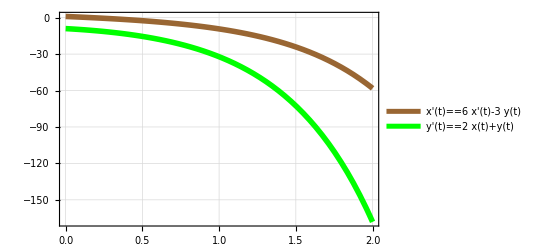

```mathematica
eq3:={x'[t]==6*x'[t] - 3*y[t], y'[t]==2*x[t]+ y[t], x[0]==1, y[0]==-9};
DSolve[eq3, {x[t],y[t]}, t]
Plot[Evaluate[{x[t],y[t]} /. %], {t,0,2},PlotLegends->{eq3},PlotStyle->{{Brown,Thickness[0.01]},{Green,Thickness[0.01]}},Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed]]
```

## Question 4 : x’[t]==6*x’[t] - 3*y[t]+ z[t] y’[t]==2*x[t]+ y[t]-6*z[t] y[t]+56*x[t]==z’[t]

{{x[t]→-8 RootSum[23850+400 #1-5 #1^2+#1^3&,(85 ⅇ^((t #1)/5)+ⅇ^((t #1)/5) #1)/(400-10 #1+3 #1^2)&]-9 RootSum[23850+400 #1-5 #1^2+#1^3&,(-5 ⅇ^((t #1)/5)+3 ⅇ^((t #1)/5) #1)/(400-10 #1+3 #1^2)&]+RootSum[23850+400 #1-5 #1^2+#1^3&,(150 ⅇ^((t #1)/5)-5 ⅇ^((t #1)/5) #1+ⅇ^((t #1)/5) #1^2)/(400-10 #1+3 #1^2)&],y[t]→10 RootSum[23850+400 #1-5 #1^2+#1^3&,(-840 ⅇ^((t #1)/5)+ⅇ^((t #1)/5) #1)/(400-10 #1+3 #1^2)&]-80 RootSum[23850+400 #1-5 #1^2+#1^3&,(ⅇ^((t #1)/5)+3 ⅇ^((t #1)/5) #1)/(400-10 #1+3 #1^2)&]-9 RootSum[23850+400 #1-5 #1^2+#1^3&,(280 ⅇ^((t #1)/5)+ⅇ^((t #1)/5) #1^2)/(400-10 #1+3 #1^2)&],z[t]→-45 RootSum[23850+400 #1-5 #1^2+#1^3&,(168 ⅇ^((t #1)/5)+ⅇ^((t #1)/5) #1)/(400-10 #1+3 #1^2)&]+10 RootSum[23850+400 #1-5 #1^2+#1^3&,(-135 ⅇ^((t #1)/5)+28 ⅇ^((t #1)/5) #1)/(400-10 #1+3 #1^2)&]+8 RootSum[23850+400 #1-5 #1^2+#1^3&,(-30 ⅇ^((t #1)/5)-5 ⅇ^((t #1)/5) #1+ⅇ^((t #1)/5) #1^2)/(400-10 #1+3 #1^2)&]}}

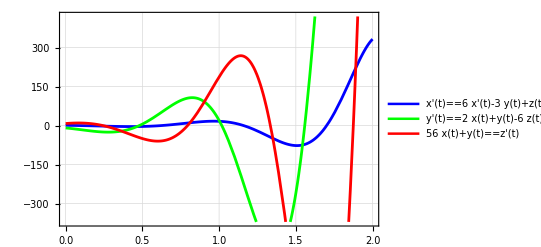

```mathematica
eq4:={x'[t]==6*x'[t] - 3*y[t]+ z[t], y'[t]==2*x[t]+ y[t]-6*z[t],y[t]+56*x[t]==z'[t], x[0]==1, y[0]==-9,z[0]==8};
DSolve[eq4, {x[t],y[t],z[t]}, t]
Plot[Evaluate[{x[t],y[t],z[t]} /. %], {t,0,2},PlotLegends->{eq4},PlotStyle->{{Blue,Thickness[0.005]},{Green,Thickness[0.005]},{Red,Thickness[0.005]}},Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed]]
```

## Question 5: x’[t]==7*x’[t]- 3*y[t], y’[t]==2*x[t]

{{x[t]→-1/4 ⅇ^-t (-11+7 ⅇ^(2 t)),y[t]→-1/2 ⅇ^-t (11+7 ⅇ^(2 t))}}

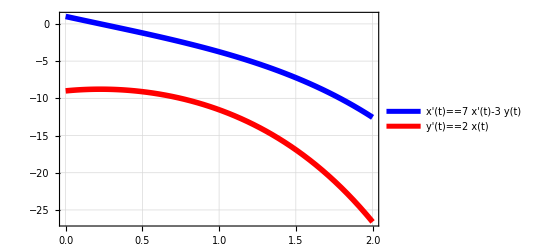

```mathematica
eq3:={x'[t]==7*x'[t]- 3*y[t], y'[t]==2*x[t], x[0]==1, y[0]==-9};
DSolve[eq3, {x[t],y[t]}, t]
Plot[Evaluate[{x[t],y[t]} /. %], {t,0,2},PlotLegends->{eq3},PlotStyle->{{Blue,Thickness[0.01]},{Red,Thickness[0.01]}},Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed]]
```

{x'[t]==y[t],y'[t]==6 x[t]-y[t],x[0]==1,y[0]==-2}

{{x[t]→1/5 ⅇ^(-3 t) (4+ⅇ^(5 t)),y[t]→2/5 ⅇ^(-3 t) (-6+ⅇ^(5 t))}}

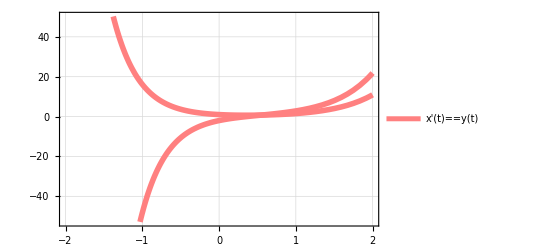

```mathematica
eq1 = {x'[t]==y[t], y'[t]==-y[t]+6*x[t], x[0]==1, y[0]==-2}
s = DSolve[eq1, {x[t],y[t]}, t]
Plot[{x[t],y[t]}/.s,{t,-2,2},PlotLegends->{eq1},PlotStyle->{{Pink,Thickness[0.01]},{Blue,Thickness[0.01]}},Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed]]
```

```mathematica
eq1
```

{x'[t]==y[t],y'[t]==6 x[t]-y[t],x[0]==1,y[0]==-2}